```mathematica
Quit[]
```

### SM Early Universe

To run simply evaluate the entire notebook SM Early Universe and look at Results

#### Documentation

The code is based upon the fact that non-thermal equilibrium corrections to the neutrino distribution functions are small. And actually, a thermal distribution function with evolving temperature ,Tν can account for the number and energy density of neutrinos very accurately. 

The result in terms of Neff in the SM is: Neff = 3.046. This is in excellent agreement with state-of-the-art calculations in the SM 1606.06986, hep-ph/0506164. In my computer the programm takes 6 seconds to run. 

The code has 4 sections.
	1-Finite Temperature Corrections: Loads the finite temperature corrections to the electromagnetic energy and pressure densities from 1 loop QED.
	2-SM Neutrino interactions with me: Loads the SM neutrino-electron and neutrino-neutrino number and energy exchanges rates. They include the effect of the electron mass. 
	3-Thermodynamics and Expansion: Defines the relevant number, energy and pressure densities for electrons, photons and neutrinos. 
	4-Temperature ODE: Defines the time evolution equations for zγ ≡ Tγ/(a m_e), and zν ≡ Tν/(a m_e).
	5-Key function. Solves zγ(a) and zν(a) 

The function FuncSMnudec[Tν0_] is the key one.
It outputs a vector containing: 
	1 Neff
	2 the asymtotic value of zγ
	3 the asymtotic value of zν
	4 Interpolating function zγ(a)
	5 Interpolating function zν(a)
	6  Interpolating function N(a)
zγ(a), zν(a)  are defined in Equation 28 of 1801.08023 and N(a) is defined in eq 60 of 1801.08023. PRIMAT uses both. 

The code is based on arXiv:1812.05605 but uses updated neutrino-neutrino and neutrino electron rates from arXiv:1907.XXXXX. All dimensionfull variables are in MeV.

#### 1-Finite Temperature Corrections

```mathematica
SetDirectory[NotebookDirectory[]];
data=Import["QED_MEV/QED_P_int.cvs","Table",HeaderLines-> 1];
Pint=Interpolation[data];
data2=Import["QED_MEV/QED_dP_intdT.cvs","Table",HeaderLines-> 1];
dPintdT:=Interpolation[data2];
data3=Import["QED_MEV/QED_d2P_intdT2.cvs","Table",HeaderLines-> 1];
d2PintdT2:=Interpolation[data3];
```

#### 2-SM Neutrino interactions with me

```mathematica
SetDirectory[NotebookDirectory[]];
data=Import["Rate_MeV/nue_ann.dat","Table",HeaderLines-> 1];
fannνe=Interpolation[data];

data=Import["Rate_MeV/nue_scatt.dat","Table",HeaderLines-> 1];
fscaνe=Interpolation[data];

data=Import["Rate_MeV/numu_ann.dat","Table",HeaderLines-> 1];
fannνμ=Interpolation[data];

data=Import["Rate_MeV/numu_scatt.dat","Table",HeaderLines-> 1];
fscaνμ=Interpolation[data];

Func[T1_,T2_]:=32 0.884*(T1^9-T2^9)+56 T1^4 T2^4*0.829*(T1-T2);

ΔρSMνe[Tγ_,Tνe_,Tνμ_]:=  GF^2/π^5((1+4 SW2 +8 SW2^2)(32 0.884*fannνe[Tγ]*(Tγ^9-Tνe^9)+56 Tγ^4 *fscaνe[Tγ]*Tνe^4*0.829*(Tγ-Tνe))+2Func[Tνμ,Tνe])/.{SW2-> 0.223}/.GF-> 1.1663787 10^-11;
ΔρSMνμ[Tγ_,Tνe_,Tνμ_]:=  GF^2/π^5((1-4 SW2 +8 SW2^2)(32 0.884*fannνμ[Tγ]*(Tγ^9-Tνμ^9)+56 Tγ^4 *fscaνμ[Tγ]*Tνμ^4*0.829*(Tγ-Tνμ))-Func[Tνμ,Tνe])/.{SW2-> 0.223}/.GF-> 1.1663787 10^-11;
```

#### 3-Thermodynamics and Expansion

```mathematica
me = 0.511;
```

```mathematica
(*Number and energy densities*)
nBE[T_,μ_]:=((2 T^3)/(2 π^2))PolyLog[3,ⅇ^(-μ/T)];
nFD[T_,μ_]:=((-2 T^3)/(2 π^2)) PolyLog[3,-ⅇ^(-μ/T)];
ρBE[T_,μ_]:=((6 T^4)/(2 π^2))PolyLog[4,ⅇ^(-μ/T)];
ρFD[T_,μ_]:=((-6 T^4)/(2 π^2)) PolyLog[4,-ⅇ^(-μ/T)];

nBEM[T_,μ_,m_]:=1/(2 π^2)T^3 NIntegrate[Enred √(Enred^2-m^2/T^2)1/(Exp[Enred-μ/T]-1),{Enred,m/T,∞}];
nFDM[T_,μ_,m_]:=1/(2 π^2)T^3 NIntegrate[Enred √(Enred^2-m^2/T^2)1/(Exp[Enred-μ/T]+1),{Enred,m/T,∞}];
nMBM[T_,μ_,m_]:=1/(2 π^2)T^3 NIntegrate[Enred √(Enred^2-m^2/T^2)1/Exp[Enred-μ/T],{Enred,m/T,∞}];
ρBEM[T_,μ_,m_]:=1/(2 π^2)T^4 NIntegrate[Enred^2 √(Enred^2-m^2/T^2)1/(Exp[Enred-μ/T]-1),{Enred,m/T,∞}];
ρFDM[T_,μ_,m_]:=1/(2 π^2)T^4 NIntegrate[Enred^2 √(Enred^2-m^2/T^2)1/(Exp[Enred-μ/T]+1),{Enred,m/T,∞}];
pBEM[T_,μ_,m_]:=1/(6 π^2)T^4 NIntegrate[(Enred^2-m^2/T^2)^(3/2)1/(Exp[Enred-μ/T]-1),{Enred,m/T,∞}];
pFDM[T_,μ_,m_]:=1/(6 π^2)T^4 NIntegrate[(Enred^2-m^2/T^2)^(3/2)1/(Exp[Enred-μ/T]+1),{Enred,m/T,∞}];

dρdTFDM[T_,μ_,m_]:=1/(2 π^2)T^3 Quiet[NIntegrate[Enred^2 √(Enred^2-m^2/T^2)((Enred -μ/T) Sech[(Enred -μ/T)/2]^2)/4,{Enred,m/T,∞}]];
Partialγe[T_]:=2 (2 π^2 T^3)/15+4dρdTFDM[T,0,me]+T d2PintdT2[T] ;


Hubble[Tγ_,Tνe_,Tνμ_,μν_,MZ_]:= √((2 ρBE[Tγ,0]+4ρFDM[Tγ,0,me]+2ρFD[Tνe,0]+4ρFD[Tνμ,μν]-Pint[Tγ]+Tγ dPintdT[Tγ]) (8 π)/(3 (1.2209 10^19 10^3)^2));

ρtot[Tγ_,Tνe_,Tνμ_,μν_,MZ_]:=(2 ρBE[Tγ,0]+4ρFDM[Tγ,0,me]+2ρFD[Tνe,0]+4ρFD[Tνμ,μν]);

ptot[Tγ_,Tνe_,Tνμ_,μν_,MZ_]:=(1/3 2 ρBE[Tγ,0]+4pFDM[Tγ,0,me]+1/3 2ρFD[Tνe,0]+4 1/3 ρFD[Tνμ,μν]);

RHSec[Tγ_,Tνe_,Tνμ_,μν_,MZ_]:=-3 Hubble[Tγ,Tνe,Tνμ,μν,MZ](ρtot[Tγ,Tνe,Tνμ,μν,MZ]+ ptot[Tγ,Tνe,Tνμ,μν,MZ]);
```

#### 4-Temperature ODE

```mathematica
m0=me;
dzγdt[zγ_,zνe_,zνμ_,μν_,g_,MZ_,a_]:=zγ/a(1/(zγ m0/a *Partialγe[zγ m0/a])(zγ m0/a *Partialγe[zγ m0/a]-4*2*ρBE[zγ m0/a,0]-3*4(ρFDM[zγ m0/a,0,me]+pFDM[zγ m0/a,0,me])-3*zγ m0/a dPintdT[zγ m0/a]-(ΔρSMνe[zγ m0/a,zνe m0/a,zνμ m0/a]+2 ΔρSMνμ[zγ m0/a,zνe m0/a,zνμ m0/a])/Hubble[zγ m0/a,zνe m0/a,zνμ m0/a,0,0]));

dzνedt[zγ_,zνe_,zνμ_,μν_,g_,MZ_,a_]:=zνe/a(ΔρSMνe[zγ m0/a,zνe m0/a,zνμ m0/a]/(4 Hubble[zγ m0/a,zνe m0/a,zνμ m0/a,0,0]*2*ρFDM[zνe m0/a,0,0]));

dzνμdt[zγ_,zνe_,zνμ_,μν_,g_,MZ_,a_]:= zνμ/a(ΔρSMνμ[zγ m0/a,zνe m0/a,zνμ m0/a]/(4 Hubble[zγ m0/a,zνe m0/a,zνμ m0/a,0,0]*2*ρFDM[zνμ m0/a,0,0]));
```

#### 5-Key function

```mathematica
FuncSMnudec[Tν0_]:=(
a0=m0/Tν0;
amax=m0/0.01;(* Tnu ~= 0.01 MeV, a time at which e+e- have annihilated away *)

solEarlyUniverse=NDSolve[{ 
zγ'[a]==dzγdt[zγ[a],zν[a],zν[a],0,0,0,a],zν'[a]==1/3(dzνedt[zγ[a],zν[a],zν[a],0,0,0,a]+2dzνμdt[zγ[a],zν[a],zν[a],0,0,0,a]),
zγ[a0]==1,zν[a0]==1},{zγ,zν},{a,a0,amax},PrecisionGoal->8,AccuracyGoal->8];

Neffres=(8/7(11/4)^(4/3)(4 ρFD[zν[a],0]+2 ρFD[zν[a],0])/(2ρBE[zγ[a],0])/.solEarlyUniverse/.{a-> amax})[[1]]//N;

zγres=(zγ[a]/.solEarlyUniverse/.{a-> amax})[[1]];
zνres=(zν[a]/.solEarlyUniverse/.{a-> amax})[[1]];

NaParthenope[a1_]:=((4/zγ[a]^4 7/8 π^2/15( 3 a/zν[a] D[zν[a],a]))/.solEarlyUniverse/.a-> a1)[[1]];

{Neffres,zγres,zνres,(zγ[a]/.solEarlyUniverse)[[1]],(zν[a]/.solEarlyUniverse)[[1]],NaParthenope[a]});
```

#### Results

N_eff = 3.04578

zγ = 1.39777

zν = 1.00146

Tγ/Tν = 1.39573

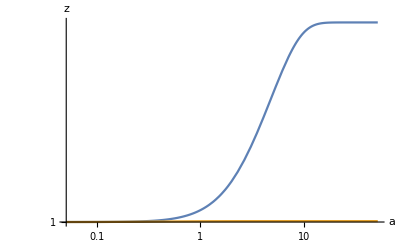

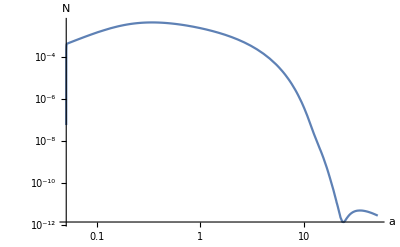

```mathematica
resultvec=Quiet[FuncSMnudec[10]];
Print["N_eff = ", resultvec[[1]]]
Print["zγ = ", resultvec[[2]]]
Print["zν = ", resultvec[[3]]]
Print["Tγ/Tν = ", resultvec[[2]]/resultvec[[3]]]

LogLogPlot[{resultvec[[4]],resultvec[[5]]},{a,a0,amax},AxesLabel->{"a","z"},PlotRange->All]

LogLogPlot[resultvec[[6]],{a,a0,amax},AxesLabel->{"a","N"}]
```